```mathematica
(* FNR(phi_ers) final formula, precomputed manually *)
```

```mathematica
Clear[d, alphaPI, pNChoPI]
```

```mathematica
betaERS := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^d;
```

```mathematica
Refine[betaERS, Assumptions-> {alphaPI==0.05, pNChoPI==0.1, d == 10}]
```

0.812969

```mathematica
simpBetaERS := Simplify[betaERS];
```

```mathematica
Assuming[{alphaPI==0.05, pNChoPI==# , d == 10}, simpBetaERS]& @ 0.03
```

0.587331

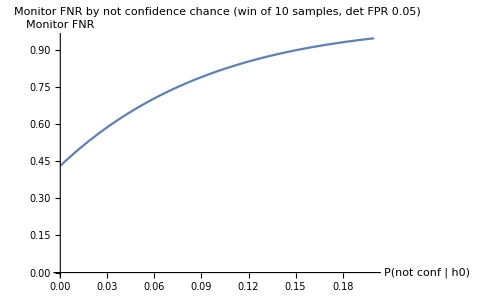

```mathematica
ListLinePlot[Assuming[{alphaPI==0.05, pNChoPI==# , d == 10}, {#, simpBetaERS}]& /@ Table[n, {n,0, 0.2, 0.001}], 
PlotLabel -> "Monitor FNR by not confidence chance (win of 10 samples, det FPR 0.05)", AxesLabel -> {"P(not conf | h0)", "Monitor FNR"}]
(*need to change what the bottom axis is*)
```

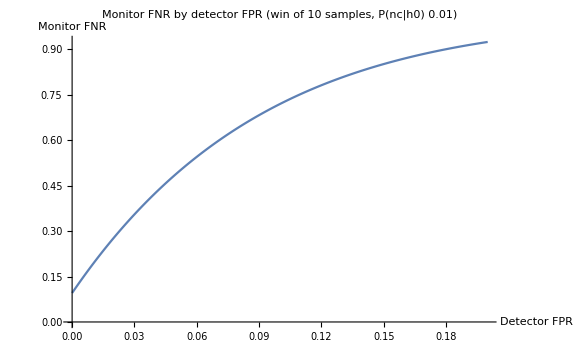

```mathematica
ListLinePlot[Assuming[{alphaPI==#, pNChoPI==0.01 , d == 10}, {#, simpBetaERS}]& /@ Table[n, {n,0, 0.2, 0.001}],
PlotLabel -> "Monitor FNR by detector FPR (win of 10 samples, P(nc|h0) 0.01)", AxesLabel -> {"Detector FPR", "Monitor FNR"}
]
(*need to change what the bottom axis is*)
```

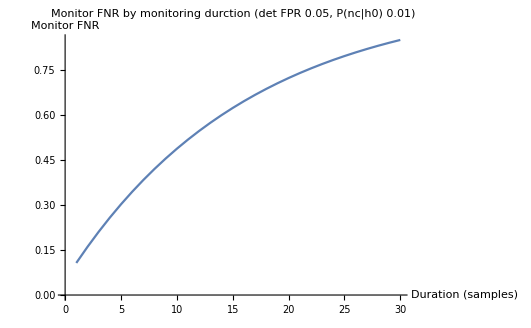

```mathematica
ListLinePlot[Assuming[{alphaPI==0.05, pNChoPI==0.01 , d == #}, {#, simpBetaERS}]& /@ Table[n, {n,1, 30, 1}], 
PlotLabel -> "Monitor FNR by monitoring durction (det FPR 0.05, P(nc|h0) 0.01)", AxesLabel -> {"Duration (samples)", "Monitor FNR"}
]
```

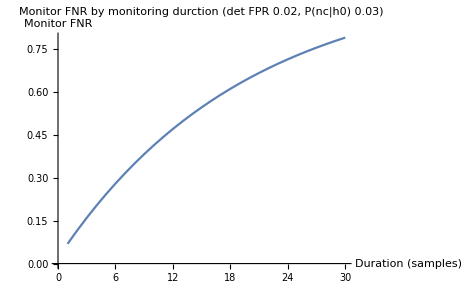

```mathematica
ListLinePlot[Assuming[{alphaPI==0.02, pNChoPI==0.03 , d == #}, {#, simpBetaERS}]& /@ Table[n, {n,1, 30, 1}], 
PlotLabel -> "Monitor FNR by monitoring durction (det FPR 0.02, P(nc|h0) 0.03)", AxesLabel -> {"Duration (samples)", "Monitor FNR"}
]
```

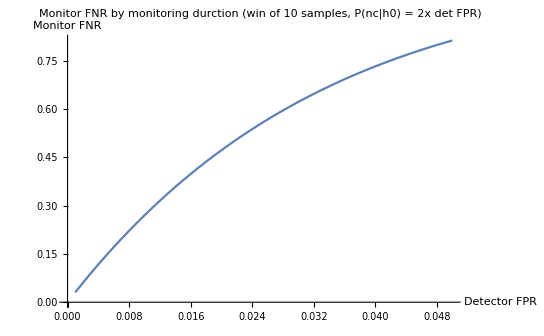

```mathematica
(* 2x linear dependency between nc and fpr of det*)
ListLinePlot[Assuming[{alphaPI==#, pNChoPI==2*#, d == 10}, {#, simpBetaERS}]& /@ Table[n, {n,0.001, 0.05, 0.001}], 
PlotLabel -> "Monitor FNR by monitoring durction (win of 10 samples, P(nc|h0) = 2x det FPR)", AxesLabel -> {"Detector FPR", "Monitor FNR"}
]
```

```mathematica
(*actual stuff that works, but the vars have to be undefined. Could also work with an Assuming outer block. *)
```

```mathematica
Simplify[betaERS, {alphaPI==0.02, pNChoPI==0.04, d == 10}]
```

betaERS

```mathematica
(*** COMPARISON WITH THE AUTOMATED CALCULATION, looks correct ***)
```

```mathematica
Refine[betaERS, Assumptions-> {alphaPI==0.1, pNChoPI==0.05, d == 1}]
```

0.235